Calculate the probablity of error using simulation data for both the fixed and theoretical optimum decision region boundaries.

```mathematica
SetDirectory[ParentDirectory[ParentDirectory[ParentDirectory[$UserBaseDirectory]]]]
simdata= Get["simout2.txt"][[2;;]]+Get["simout3.txt"][[2;;]];
Dimensions[simdata]
```

C:\Users\DonnellyY

{10,2,602}

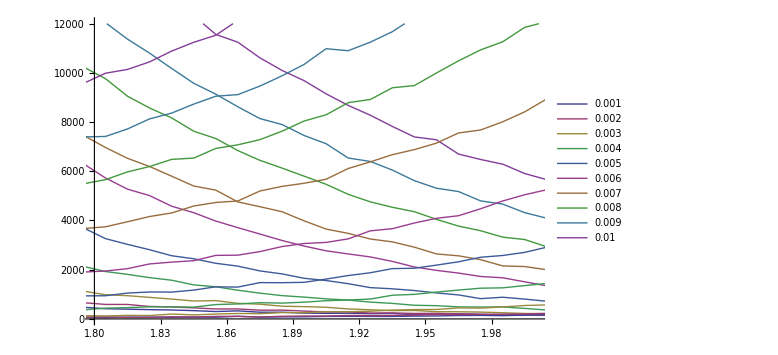

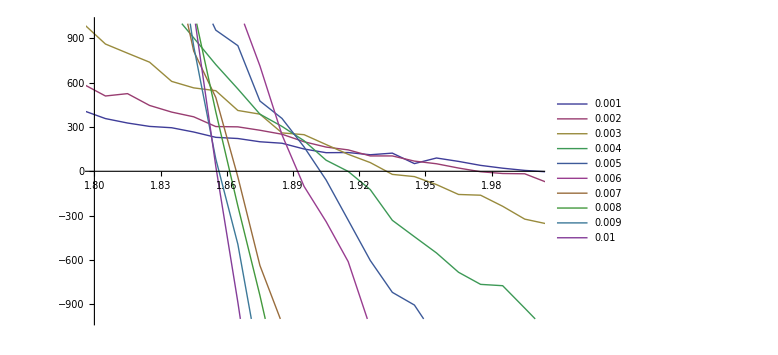

```mathematica
Show[ListLinePlot[simdata[[All,1]],ImageSize->Large,DataRange->{-1.005,5.005},PlotRange->{{1.8,2},{0,12000}},PlotLegends->Range[.001,.01,.001]],ListLinePlot[simdata[[All,2]],ImageSize->Large,DataRange->{-1.005,5.005},PlotRange->{{1.8,2},{0,12000}}]]
ListLinePlot[simdata[[All,1]]-simdata[[All,2]],ImageSize->Large,DataRange->{-1.005,5.005},PlotRange->{{1.8,2},{-1000,1000}},PlotLegends->Range[.001,.01,.001]]
```

```mathematica
Export["MRC2_odrb_PDF.png",%418,ImageResolution->300]; Export["MRC2_odrb_diff.png",%419,ImageResolution->450];
```

```mathematica
Range[-1.005,5.005,0.01][[301]]
```

1.995

```mathematica
odrb=Table[x=100;While[simdata[[p,1,x]]>simdata[[p,2,x]],x=x+1];x,{p,10}];
Table[Range[-1.005,5.005,0.01][[o]],{o,odrb}]
peo = Table[N[(Total[simdata[[p,1,302;;]]]+Total[simdata[[p,2,;;301]]])/50000000],{p,10}];
pen = Table[N[(Total[simdata[[p,1,odrb[[p]];;]]]+Total[simdata[[p,2,;;odrb[[p]]-1]]])/50000000],{p,10}];
pei = 100*(peo-pen)/peo;
Grid[Join[{{"var","Pe drb=2", "Pe opt drb","Pe Imp %"}},Transpose[N[{Range[0.001,0.01,0.001],peo,pen,pei},2]]]]
```

{2.005,1.975,1.935,1.915,1.905,1.895,1.865,1.865,1.865,1.865}

var | Pe drb=2 | Pe opt drb | Pe Imp %
0.001 | 0.00014918 | 0.00014918 | 0.
0.002 | 0.00016912 | 0.00016842 | 0.413907
0.003 | 0.0002672 | 0.00024666 | 7.68713
0.004 | 0.00059364 | 0.00050154 | 15.5145
0.005 | 0.001275 | 0.0010655 | 16.4314
0.006 | 0.00266896 | 0.00228718 | 14.3044
0.007 | 0.00508402 | 0.0041751 | 17.878
0.008 | 0.00795306 | 0.00671142 | 15.6121
0.009 | 0.0109417 | 0.00942062 | 13.9017
0.01 | 0.0149371 | 0.0130387 | 12.7091

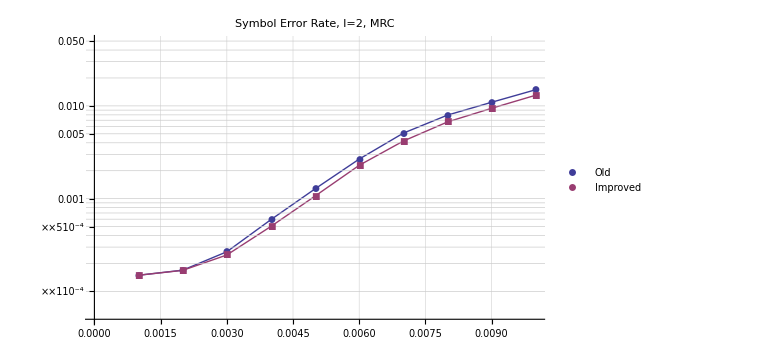

```mathematica
xvar=Range[0.001,0.01,0.001];
ListLogPlot[{Partition[Riffle[xvar,peo],{2}],Partition[Riffle[xvar,pen],{2}]},PlotRange->{5*10^-5,5*10^-2},PlotLabel->"Symbol Error Rate, l=2, MRC",PlotLegends->{"Old","Improved"},GridLines->Automatic,GridLinesStyle->GrayLevel[0.8],Joined->True,PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Export["MRC2_SER.png",%,ImageResolution->400]
```

MRC2_SER.png